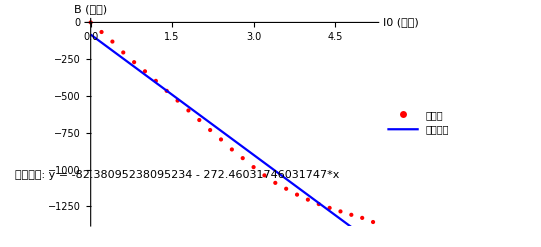

拟合方程: -82.381-272.46 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | -82.381 | 24.9766 | -3.29833 | 0.00291726
x | -272.46 | 8.24051 | -33.0635 | 3.72344×10^-22

决定系数R.b2：0.977643

标准误差：4449.2

计算得出的斜率: -272.46

相关系数r: -0.988758

```mathematica
(*定义数据数组*)I0={0.00,0.20,0.40,0.60,0.80,1.00,1.20,1.40,1.60,1.80,2.00,2.20,2.40,2.60,2.80,3.00,3.20,3.40,3.60,3.80,4.00,4.20,4.40,4.60,4.80,5.00,5.20};
B={0,-65,-130,-204,-270,-332,-397,-465,-531,-598,-663,-731,-795,-863,-922,-983,-1039,-1090,-1130,-1170,-1204,-1234,-1260,-1284,-1307,-1328,-1356};

(*线性回归拟合*)
fit=LinearModelFit[Transpose[{I0,B}],x,x];

(*获取拟合方程和斜率*)
fitFunction=fit["BestFit"];
slope=fit["BestFitParameters"][[2]];

(*计算相关系数*)
r=Correlation[I0,B];

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[Transpose[{I0,B}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"I0 (单位)","B (单位)"},PlotLegends->{"数据点"}],Plot[fitFunction,{x,Min[I0],Max[I0]},PlotStyle->Blue,PlotLabel->"一次线性拟合曲线",PlotLegends->{"拟合曲线"}],Epilog->Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{1.6,-1000},{0,1}]]

(*输出拟合方程、相关系数和误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
Print["计算得出的斜率: ",slope];
Print["相关系数r: ",r];
```

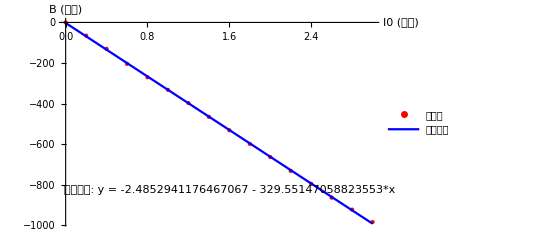

拟合方程: -2.48529-329.551 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.48529 | 1.71999 | -1.44494 | 0.170483
x | -329.551 | 0.97689 | -337.348 | 8.92458×10^-29

决定系数R.b2：0.999877

标准误差：12.9787

计算得出的斜率: -329.551

相关系数r: -0.999938

```mathematica
(*定义数据数组*)I0={0.00,0.20,0.40,0.60,0.80,1.00,1.20,1.40,1.60,1.80,2.00,2.20,2.40,2.60,2.80,3.00};
B={0,-65,-130,-204,-270,-332,-397,-465,-531,-598,-663,-731,-795,-863,-922,-983};

(*线性回归拟合*)
fit=LinearModelFit[Transpose[{I0,B}],x,x];

(*获取拟合方程和斜率*)
fitFunction=fit["BestFit"];
slope=fit["BestFitParameters"][[2]];

(*计算相关系数*)
r=Correlation[I0,B];

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[Transpose[{I0,B}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"I0 (单位)","B (单位)"},PlotLegends->{"数据点"}],Plot[fitFunction,{x,Min[I0],Max[I0]},PlotStyle->Blue,PlotLabel->"一次线性拟合曲线",PlotLegends->{"拟合曲线"}],Epilog->Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{1.6,-800},{0,1}]]

(*输出拟合方程、相关系数和误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
Print["计算得出的斜率: ",slope];
Print["相关系数r: ",r];
```

```mathematica
(9.868-8.239)*1.9
```

```mathematica
3.095099999999999/60
```

0.051585

```mathematica
0.054/(0.332*0.502)
```

0.324005

```mathematica
3.095099999999999/(0.332*0.502)
```

18.5709

```mathematica
-2.4852941176467067-329.55147058823553*1.4
```

-463.857

```mathematica
-2.4852941176467067-329.55147058823553*1.8
```

-595.678

```mathematica
(1.117-0.388)*1.9/((596-464)*10^{-3}*0.502)
```

{20.9028}